```mathematica
DSolve[y''[x]+y'[x]+U1*E+(U0-U1*E)*E^(-x)==0,y,x]
```

{{y→Function[{x},-ⅇ U1 x+ⅇ^-x (U0-ⅇ U1+(U0-ⅇ U1) x-C[1])+C[2]]}}

```mathematica
f[x_]=-ⅇ U1 x+ⅇ^-x (U0-ⅇ U1+(U0-ⅇ U1) x-(U1*E+U0-ⅇ U1))+U1*E
```

ⅇ U1-ⅇ U1 x+ⅇ^-x (-ⅇ U1+(U0-ⅇ U1) x)

```mathematica
Expand[%9]
```

```mathematica
ⅇ U1-ⅇ^(1-x) U1-ⅇ U1 x-ⅇ^(1-x) U1 x//Simplify
```

-ⅇ^(1-x) U1 (1+ⅇ^x (-1+x)+x)

```mathematica
5/1.414
```

3.53607

```mathematica
Cases[ⅇ U1-ⅇ^(1-x) U1+ⅇ^-x U0 x-ⅇ U1 x-ⅇ^(1-x) U1 x,_*U1]
```

{ⅇ U1,-ⅇ^(1-x) U1,-ⅇ U1 x,-ⅇ^(1-x) U1 x}

```mathematica
Plus@@%3/E
```

(ⅇ U1-ⅇ^(1-x) U1-ⅇ U1 x-ⅇ^(1-x) U1 x)/ⅇ

```mathematica
Simplify[(ⅇ U1-ⅇ^(1-x) U1-ⅇ U1 x-ⅇ^(1-x) U1 x)/(ⅇ*U1)]
```

-ⅇ^-x (1+ⅇ^x (-1+x)+x)

```mathematica
Expand[%]
```

```mathematica
-ⅇ^-x-ⅇ^-x x
```

```mathematica
f[0]
```

U0-ⅇ U1-C[1]+C[2]

```mathematica
Solve[%==0&&C[2]==0,
```

```mathematica
-ⅇ U1 x+ⅇ^-x (U0-ⅇ U1+(U0-ⅇ U1) x-C[1])+C[2]
```

```mathematica
D[f[x],{x,2}]+D[f[x],x]+U1*E+(U0-U1*E)*E^(-x)//Simplify
```

0

```mathematica
1000/42.778-3.02
```

20.3565

```mathematica
1/(2*3.14*(89.43-88.7))
```

0.218131

```mathematica
1/((2*3.14*89.01)^2*0.22)
```

0.0000145472

```mathematica
%*1000
```

0.0145472

```mathematica
1.404*(1+3.02/20.36)/(2*3.14*89.01)
```

0.00288427

```mathematica
(2*3.14*89.01*0.22)/20.36
```

6.04009

```mathematica
list=Range[0,90,10]
```

```mathematica
list={0,10,20,30,40,50,60,70,80,90,33,35}
```

{0,10,20,30,40,50,60,70,80,90,33,35}

```mathematica
list2={0.592,0.55,0.516,0.512,0.516,0.516,0.516,0.520,0.520,0.528}
list3={0.935,1.075,1.145,1.145,1.115,1.090,1.040,0.990,0.990,0.990}
```

{0.592,0.55,0.516,0.512,0.516,0.516,0.516,0.52,0.52,0.528}

{0.935,1.075,1.145,1.145,1.115,1.09,1.04,0.99,0.99,0.99}

```mathematica
list4={};For[i=1,i<=10,i++,AppendTo[list4,(list3[[i]]/list2[[i]]-1)*16]]
```

```mathematica
list4
```

{9.27027,15.2727,19.5039,19.7813,18.5736,17.7984,16.2481,14.4615,14.4615,14.}

```mathematica
AppendTo[list4,(1.145/0.51-1)*16]
```

{9.27027,15.2727,19.5039,19.7813,18.5736,17.7984,16.2481,14.4615,14.4615,14.,19.642,19.9216}

```mathematica
(3.14*0.988^2*5)/1.008
```

15.2038

```mathematica
2*3.14*5*1.008
```

31.6512

```mathematica
Length[list]
```

10

```mathematica
list4=list4-4.56
```

{4.71027,10.7127,14.9439,15.2213,14.0136,13.2384,11.6881,9.90154,9.90154,9.44,15.082,15.3616}

```mathematica
Length[list4]
```

11

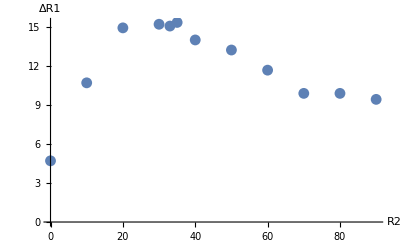

```mathematica
ListPlot[{list,list4}//Transpose,AxesLabel->{"R2","ΔR1"}]
```

```mathematica
Interpolation[{list,list4}//Transpose]
```

InterpolatingFunction[{{0., 90.}}, <>]

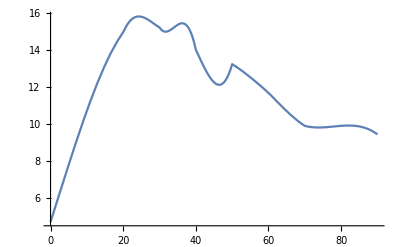

```mathematica
Plot[%42[x],{x,0.,90.}]
```

```mathematica
list=Range[0,80,10]
```

{0,10,20,30,40,50,60,70,80}

```mathematica
list2={0.596,0.548,0.526,0.514,0.514,0.518,0.524,0.524,0.528}
list3={0,0.204,0.355,0.5,0.61,0.715,0.81,0.84,0.89}
```

{0.596,0.548,0.526,0.514,0.514,0.518,0.524,0.524,0.528}

{0,0.204,0.355,0.5,0.61,0.715,0.81,0.84,0.89}

```mathematica
list4={};For[i=1,i≤9,i++,AppendTo[list4,16*list3[[i]]/(2*3.14*5*list2[[i]])]]
```

```mathematica
list4
```

{0.,0.189688,0.343901,0.495675,0.604724,0.703342,0.78767,0.816843,0.858908}

```mathematica
list4=0.965-list4
```

{0.965,0.775312,0.621099,0.469325,0.360276,0.261658,0.17733,0.148157,0.106092}

```mathematica
0.01*70*Log[1+12/7]
```

0.69897

```mathematica
%*5/7
```

0.499264

```mathematica
100/15//N
```

6.66667

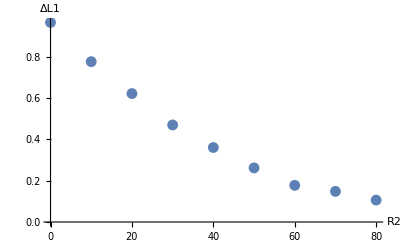

```mathematica
ListPlot[{list,list4}//Transpose,AxesLabel->{"R2","ΔL1"}]
```

```mathematica
listU={0,0.097,0.192,0.306,0.399,0.495,0.6,0.696,0.799,0.916,1.104,1.305,1.522,1.698,2.041,2.34,2.647,2.952,3.652,4.799,5.435,6.331,6.442,6.481,6.518,6.584,6.821,6.966,7.065,7.136,7.189,7.265,7.316,7.433,7.5,7.541,7.544}
listI={-0.28,-0.102,-0.175,-0.262,-0.332,-0.405,-0.485,-0.558,-0.637,-0.726,-0.853,-0.935,-1.025,-1.097,-1.239,-1.362,-1.489,-1.614,-1.903,-2.377,-2.639,-2.994,-2.725,-2.63,-2.542,-2.382,-1.812,-1.462,-1.225,-1.054,-0.925,-0.744,-0.621,-0.341,-0.180,-0.082,-0.075}
```

{0,0.097,0.192,0.306,0.399,0.495,0.6,0.696,0.799,0.916,1.104,1.305,1.522,1.698,2.041,2.34,2.647,2.952,3.652,4.799,5.435,6.331,6.442,6.481,6.518,6.584,6.821,6.966,7.065,7.136,7.189,7.265,7.316,7.433,7.5,7.541,7.544}

{-0.28,-0.102,-0.175,-0.262,-0.332,-0.405,-0.485,-0.558,-0.637,-0.726,-0.853,-0.935,-1.025,-1.097,-1.239,-1.362,-1.489,-1.614,-1.903,-2.377,-2.639,-2.994,-2.725,-2.63,-2.542,-2.382,-1.812,-1.462,-1.225,-1.054,-0.925,-0.744,-0.621,-0.341,-0.18,-0.082,-0.075}

```mathematica
Length/@{listU,listI}
```

{37,37}

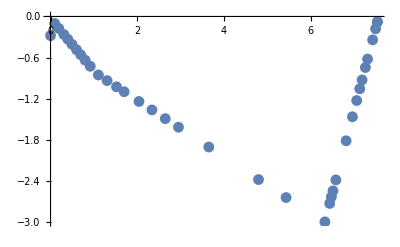

```mathematica
ListPlot[{listU,listI}//Transpose]
```